# 迷宫生成器

创建随机迷宫 .

```mathematica
(*custom styling*)style={Background->GrayLevel[0],BaseStyle->{Directive[White,EdgeForm[],Opacity[1]]},VertexShapeFunction->(Rectangle[#1+.16,#1-.16]&),EdgeShapeFunction->(Rectangle[#1[[1]]+.16,#1[[2]]-.16]&)};
embedding=GraphEmbedding[GridGraph[{20,30}]];
```

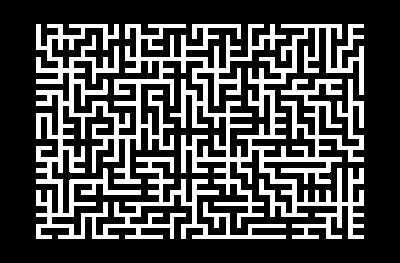

```mathematica
g=GridGraph[{20,30},EdgeWeight->RandomReal[10,1150]];
tree=FindSpanningTree[{g,1}];
maze=Graph[tree,VertexCoordinates->embedding,style]
```

解迷宫并突出显示路径 .

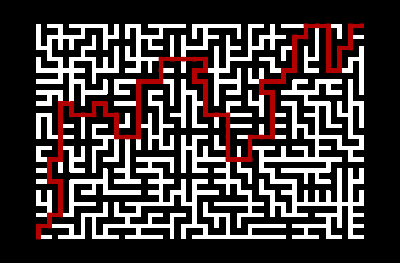

```mathematica
HighlightGraph[maze,PathGraph[FindShortestPath[maze,1,600]]]
```

使用循环生成迷宫图案

```mathematica
genLines[width_,height_,step_]:=Module[{lines={}},(For[i=0,i<width,i+=step,
For[j=0,j<height,j+=step,
If[RandomInteger[]==1,
AppendTo[lines,{{i,j},{i+step,j+step}}],
AppendTo[lines,{{i+step,j},{i,j+step}}]
]
]];lines)]
```

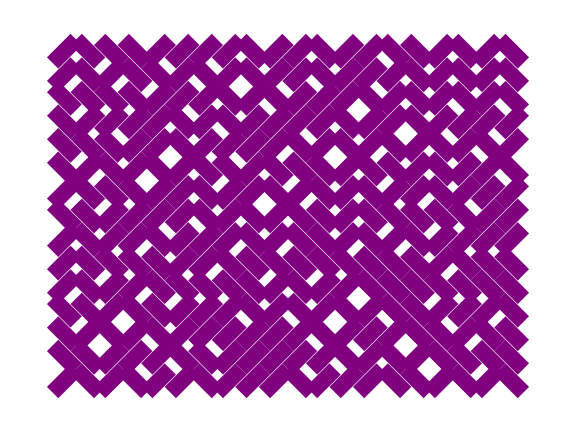

```mathematica
lines=genLines[200,150,10];
g=Graphics[{Thickness[0.02],Purple,Line[lines]},ImageSize->Large]
```